```mathematica
SetDirectory[NotebookDirectory[]];
log=False;
If[log==True,lp="ListLogLogPlot";p="LogLogPlot";,lp="ListPlot";p="Plot";]
```

{16575.7,16888.6,20072.7,24227.8}

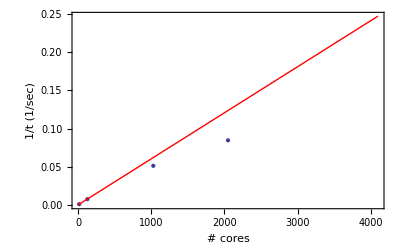

```mathematica
data=Import["elap10000.out"];
xdata=Transpose[data][[1]];
xdata*Transpose[data][[2]]
ydata=1/Transpose[data][[2]];
plotdata=Transpose[{xdata,ydata}];
p1=ToExpression[lp][plotdata,Frame->{{True,False},{True,False}},FrameLabel->{"# cores","1/t (1/sec)"},FrameStyle->15,PlotRange->All];
slope=plotdata[[1]][[2]]/plotdata[[1]][[1]];
p2=ToExpression[p][slope*x,{x,0.0001,4096},PlotStyle->Red];
Show[p1,p2]
```

{13915.4,13961.7,14085.1,14309.4}

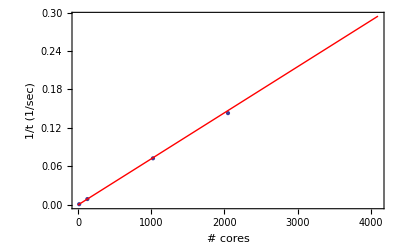

```mathematica
data=Import["test.out"];
xdata=Transpose[data][[1]];
xdata*Transpose[data][[2]]
ydata=1/Transpose[data][[2]];
plotdata=Transpose[{xdata,ydata}];
p1=ToExpression[lp][plotdata,Frame->{{True,False},{True,False}},FrameLabel->{"# cores","1/t (1/sec)"},FrameStyle->15,PlotRange->All];
slope=plotdata[[1]][[2]]/plotdata[[1]][[1]];
p2=ToExpression[p][slope*x,{x,0.0001,4096},PlotStyle->Red];
Show[p1,p2]
```

{7655.05,7684.64,8068.48,13289.5,14016.5,16613.4}

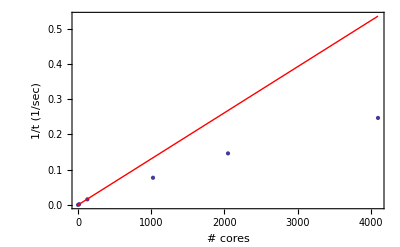

```mathematica
data=Import["oldelap10000.out"];
xdata=Transpose[data][[1]];
xdata*Transpose[data][[2]]
ydata=1/Transpose[data][[2]];
plotdata=Transpose[{xdata,ydata}];
p1=ToExpression[lp][plotdata,Frame->{{True,False},{True,False}},FrameLabel->{"# cores","1/t (1/sec)"},FrameStyle->15,PlotRange->All];
slope=plotdata[[1]][[1]]*plotdata[[1]][[2]];
p2=ToExpression[p][slope*x,{x,0.0001,4096},PlotStyle->Red];
Show[p1,p2]
```

{3391.64,3431.66,3667.84}

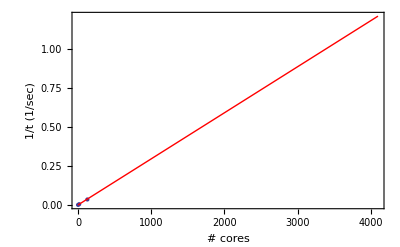

```mathematica
data=Import["oldelap4096.out"];
xdata=Transpose[data][[1]];
xdata*Transpose[data][[2]]
ydata=1/Transpose[data][[2]];
plotdata=Transpose[{xdata,ydata}];
p1=ToExpression[lp][plotdata,Frame->{{True,False},{True,False}},FrameLabel->{"# cores","1/t (1/sec)"},FrameStyle->15,PlotRange->All];
slope=plotdata[[1]][[1]]*plotdata[[1]][[2]];
p2=ToExpression[p][slope*x,{x,0.0001,4096},PlotStyle->Red];
Show[p1,p2]
```